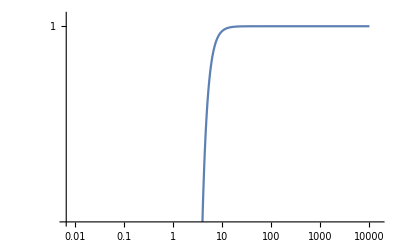

```mathematica
S[M_]:=1-(1/M)^4;
LogLogPlot[S[M], {M,0.01,10^4}]
```

1.8

{0.001,0.1}

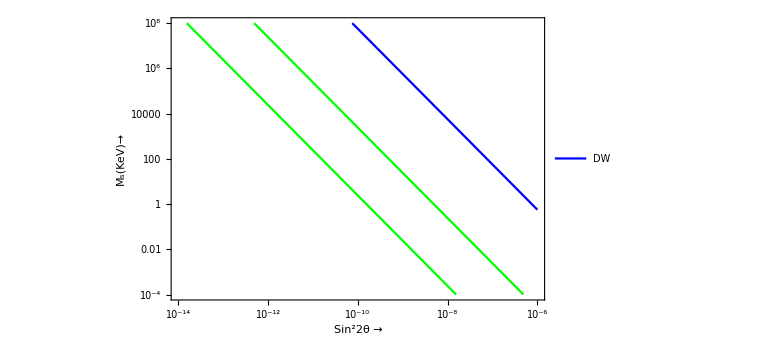

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

example1.png

```mathematica
x=1.8
L={0.001,0.1}
L1=10^-6;
g=10.75;
M[S_]:= (7.5*10^-10*L^(-3/4)*(10)^(-3/2)*x^(1/4)*(g/10.75)^0.5/S)^2;
M1[S_]:= (7.5*10^-10*L1^(-3/4)*(10)^(-3/2)*(g/10.75)^0.5/S)^2;
LogLogPlot[M[S], {S, 10^-14,10^-6}, PlotRange->{{10^-14,10^-6},{10^-4, 10^8}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"Sin^22θ →","M_s(KeV)→"},PlotStyle->Green, LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[M1[S], {S, 10^-14,10^-6}, PlotRange->{{10^-14,10^-6},{10^-4, 10^8}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"Sin^22θ →","M_s(KeV)→"},PlotStyle->Blue, PlotLegends->{"DW","MSW"}, LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
y=Show[%,%%]
Export["example1.png",Plot[y]]
```

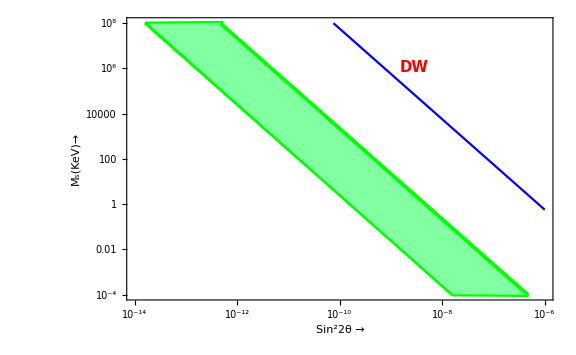

1

{0.0001,0.1}

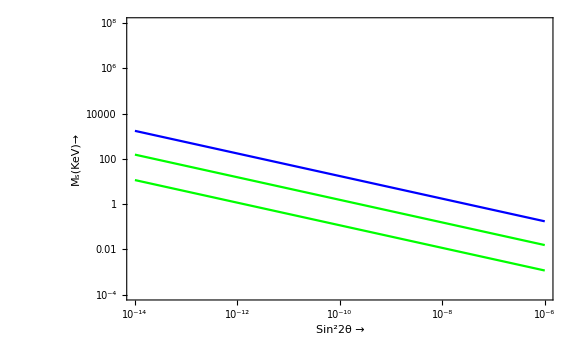

```mathematica
x=1
L={0.0001,0.1}

g=10.75;
M[S_]:= (7.5*10^-12*L^(-3/4)*(10)^(-3/2)*x/S)^0.5;

Y[S_]:=(3*10^-8/S)^0.5;
LogLogPlot[M[S], {S, 10^-14,10^-6}, PlotRange->{{10^-14,10^-6},{10^-4, 10^8}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"Sin^22θ →","M_s(KeV)→"},PlotStyle->Green, LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Y[S], {S, 10^-14,10^-6}, PlotRange->{{10^-14,10^-6},{10^-4, 10^8}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"Sin^22θ →","M_s(KeV)→"},PlotStyle->Blue, LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];

y=Show[%,%%]
```

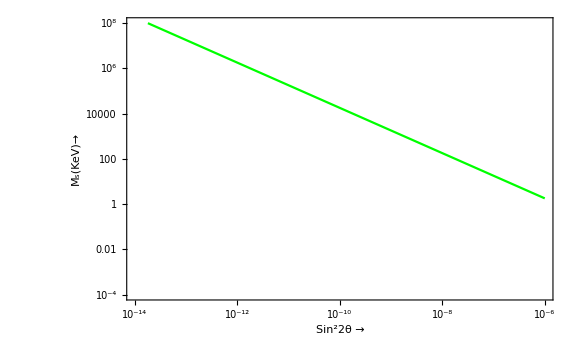

```mathematica
L=10^-15;
M[S_]:= (1/0.1245^0.5)(L/10^-2)^0.5(1/(S/2));
LogLogPlot[M[S], {S, 10^-14,10^-6}, PlotRange->{{10^-14,10^-6},{10^-4, 10^8}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"Sin^22θ →","M_s(KeV)→"},PlotStyle->Green, LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

```mathematica
ListLogLogPlot[{{100,5*10^-12},{1,10^-7}},PlotRange->{{1,100},{10^-14, 10^-7}},FrameLabel->{"M_s(KeV)→","Sin^22θ →"},Joined->True,PlotLegends->{"L=10^-12"},Frame-> True,PlotStyle->Red,  FrameTicksStyle->Directive[Black,15],LabelStyle->Directive[Black,Bold, Medium,15],ImageSize->Large];
ListLogLogPlot[{{100,10^-13},{1,10^-9}},PlotRange->{{1,100},{10^-14, 10^-7}},FrameLabel->{"M_s(KeV)→","Sin^22θ →"},Joined->True,PlotLegends->{"L=10^-3"},Frame-> True,PlotStyle->Blue,  FrameTicksStyle->Directive[Black,15],LabelStyle->Directive[Black,Bold, Medium,15],ImageSize->Large];
Show[%,%%]
```

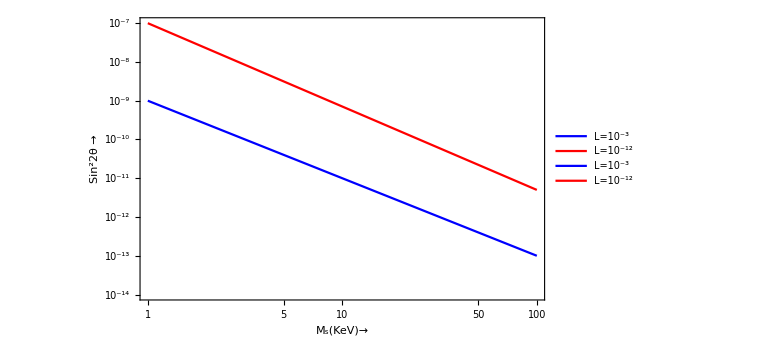

```mathematica
ListLogLogPlot[{{1,10^-7},{2.02,10^-7},{3,2*10^-8},{3.1,4*10^-9},{3.5,3.88*10^-9},{42,2*10^-13},{50,2*10^-14}},Joined->True,Filling->Top, Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"M_s(KeV)→","Sin^22θ →"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
ListLogLogPlot[{{100,5*10^-12},{1,10^-7}},PlotRange->{{1,50},{10^-14, 10^-7}},FrameLabel->{"M_s(KeV)→","Sin^22θ →"},Joined->True,PlotLegends->{"L=10^-12"},Frame-> True,PlotStyle->Red,  FrameTicksStyle->Directive[Black,15],LabelStyle->Directive[Black,Bold, Medium,15],ImageSize->Large];
ListLogLogPlot[{{100,10^-13},{1,10^-9}},PlotRange->{{1,50},{10^-14, 10^-7}},FrameLabel->{"M_s(KeV)→","Sin^22θ →"},Joined->True,PlotLegends->{"L=10^-3"},Frame-> True,PlotStyle->Blue,  FrameTicksStyle->Directive[Black,15],LabelStyle->Directive[Black,Bold, Medium,15],ImageSize->Large];
Show[%,%%,%%%]
```